```mathematica
直角坐标和极坐标两种方法的能量误差比较:机器精度
```

E0= -0.0735

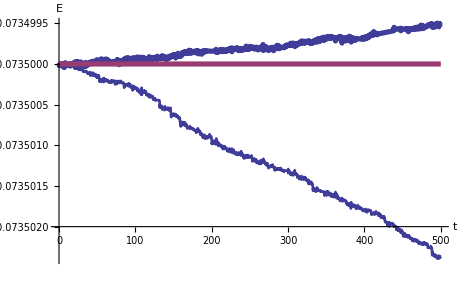

```mathematica
g=98/10;k=1/10;m=1/50;L0=1;tm=500;
θinitial={0,7/2/L0};
Linitial={L0,0};
xinitial={0,7/2};
yinitial={-L0,0};
Print["E0= ",E0=m xinitial[[2]]^2/2.0-m g L0]
(*.......................................*)
equs1={L[t] θ''[t]==-2L'[t] θ'[t]-g Sin[θ[t]],
L''[t]==-k (L[t]-L0)/m+g Cos[θ[t]]+
L[t] θ'[t]^2,
θ[0]==θinitial[[1]],θ'[0]==θinitial[[2]],
L[0]==Linitial[[1]],L'[0]==Linitial[[2]]};
s=NDSolve[equs1,{θ,L},{t,0,tm},MaxSteps->∞];
{θ,L}={θ,L}/.s[[1]];
energy[t_]:=m ((L[t]*θ'[t])^2+L'[t]^2)/2-
m g L[t] Cos[θ[t]]+k (L[t]-L0)^2/2;
g1=Plot[{energy[t],E0},{t,0,tm},
PlotStyle->Thickness[0.004]];
Clear[energy]
(*.......................................*)
equs2={x''[t]==-k x[t] (1-L0/(√(x[t]^2+y[t]^2)))/m,
y''[t]==-k y[t] (1-L0/(√(x[t]^2+y[t]^2)))/m-g,
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],
y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equs2,{x,y},{t,0,tm},MaxSteps->∞];
{x,y}={x,y}/.s[[1]];
energy[t_]:=m (x'[t]^2+y'[t]^2)/2+m g y[t]+
k (√(x[t]^2+y[t]^2)-L0)^2/2;
g2=Plot[{energy[t],E0},{t,0,tm},
PlotStyle->Thickness[0.008]];
Show[{g1,g2},AxesLabel->{"t","E"},
PlotRange->All,AxesStyle->Thickness[0.003]]
Clear[s,θ,L,energy,x,y,equs1,equs2,E0]
```

E0= -0.0735

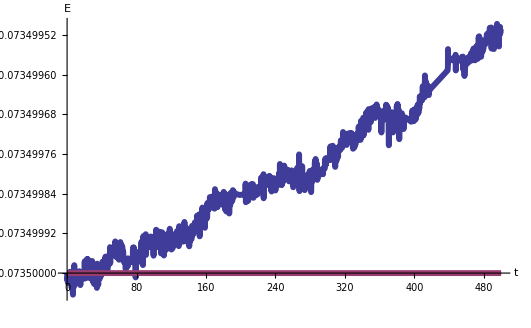

```mathematica
g=98/10;k=1/10;m=1/50;L0=1;tm=500;
θinitial={0,7/2/L0};
Linitial={L0,0};
xinitial={0,7/2};
yinitial={-L0,0};
Print["E0= ",E0=m xinitial[[2]]^2/2.0-m g L0]
(*.......................................*)
equs1={L[t] θ''[t]==-2L'[t] θ'[t]-g Sin[θ[t]],
L''[t]==-k (L[t]-L0)/m+g Cos[θ[t]]+
L[t] θ'[t]^2,
θ[0]==θinitial[[1]],θ'[0]==θinitial[[2]],
L[0]==Linitial[[1]],L'[0]==Linitial[[2]]};
s=NDSolve[equs1,{θ,L},{t,0,tm},MaxSteps->∞,WorkingPrecision->30];
{θ,L}={θ,L}/.s[[1]];
energy[t_]:=m ((L[t]*θ'[t])^2+L'[t]^2)/2-
m g L[t] Cos[θ[t]]+k (L[t]-L0)^2/2;
g1=Plot[{energy[t],E0},{t,0,tm},
PlotStyle->Thickness[0.004]];
Clear[energy]
(*.......................................*)
equs2={x''[t]==-k x[t] (1-L0/(√(x[t]^2+y[t]^2)))/m,
y''[t]==-k y[t] (1-L0/(√(x[t]^2+y[t]^2)))/m-g,
x[0]==xinitial[[1]],x'[0]==xinitial[[2]],
y[0]==yinitial[[1]],y'[0]==yinitial[[2]]};
s=NDSolve[equs2,{x,y},{t,0,tm},MaxSteps->∞];
{x,y}={x,y}/.s[[1]];
energy[t_]:=m (x'[t]^2+y'[t]^2)/2+m g y[t]+
k (√(x[t]^2+y[t]^2)-L0)^2/2;
g2=Plot[{energy[t],E0},{t,0,tm},
PlotStyle->Thickness[0.008]];
Show[{g1,g2},AxesLabel->{"t","E"},
PlotRange->All,AxesStyle->Thickness[0.003]]
Clear[s,θ,L,energy,x,y,equs1,equs2,E0]
```

```mathematica
极坐标系下验证弹簧摆的能量守恒:高精度
```

-0.0735

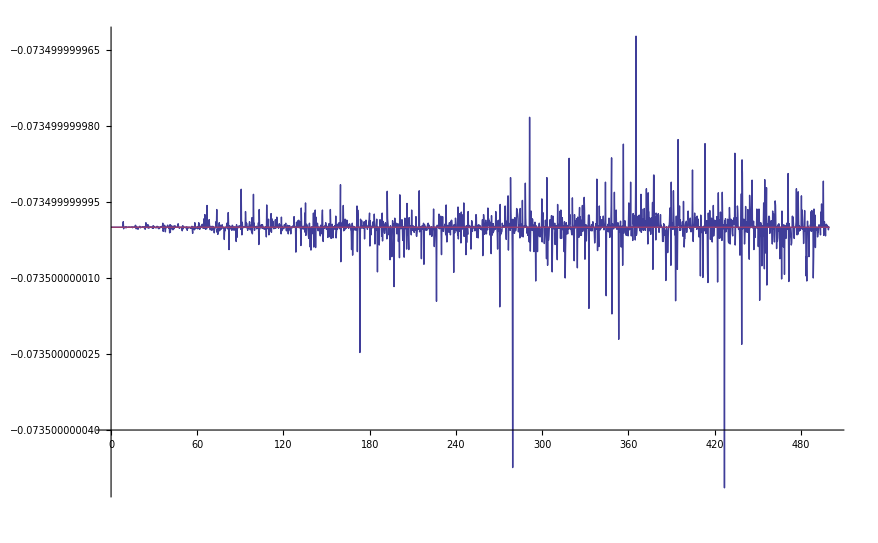

```mathematica
g=98/10;k=1/10;m=1/50;L0=1;
θinitial={0,7/2/L0};Linitial={L0,0};
tm=500;E0=1/2*m*3.5^2-m g L0
equ={L[t] θ''[t]==-2 L'[t] θ'[t]-g Sin[θ[t]],
L''[t]==-k/m (L[t]-L0)+g Cos[θ[t]]+L[t] θ'[t]^2,
θ[0]==θinitial[[1]],θ'[0]==θinitial[[2]],
L[0]==Linitial[[1]],L'[0]==Linitial[[2]]};
s=NDSolve[equ,{θ,L},{t,0,tm},
WorkingPrecision->40,MaxSteps->∞];
{θ,L}={θ,L}/.s[[1]];
energy[t_]:=1/2 m (L'[t]^2+L[t]^2 θ'[t]^2)-
m g L[t] Cos[θ[t]]+1/2 k (L[t]-L0)^2;
Plot[{energy[t],E0},{t,0,tm},PlotRange->All,
Axes->{False,True},PlotPoints->1000]
Clear[g,k,m,L0,θinitial,Linitial,tm,
equ,s,θ,L,energy,E0]
```